```mathematica
SetOptions[SelectedNotebook[],FontProperties->{"ScreenResolution"->Automatic}];
```

```mathematica
Include/@{"Hamiltonian.nb","Wave.nb"};
```

```mathematica
Unprotect[KroneckerProduct];
KroneckerProduct[x_]:=x;
Protect[KroneckerProduct];

DefLabel={_?AtomQ,___}|_?AtomQ|(Except[List,_Symbol][___]);
DefPattern={DefLabel,_List:{}};
SegmentPattern={DefPattern..,Except[_List]};
DefOrSegment=DefPattern|SegmentPattern;

ClearAll[Frequency,Strength];
Frequency@{args__}:=Frequency[args];
Strength@{args__}:=Strength[args];
Strength[__]=1;
```

```mathematica
ClearAll[Rabi,Omega,Coupling,Amplitude,Formula];
Rabi[label:DefLabel]:=Amplitude@label Strength@label;
Rabi[args__]:=Rabi@{args};
Omega[label:DefLabel,t_:Global`t]:=Exp[-ⅈ 2π Frequency@label t] Strength@label;
Omega[args__]:=Omega@{args};

Coupling[{args__}]:=Coupling[args];
Coupling[n_Integer,{i_Integer,j_Integer,k__Integer}]:=KroneckerProduct[Sequence@@ReplacePart[ConstantArray[NIdentity,NNumber],n->(*i@1.j@1*)CouplingMatrix[NDimension,{i,j}]],Sequence@@(PhononOperations⟦#+2⟧&/@PadRight[{-k},MNumber])];
Coupling[n_Integer,{i_Integer,j_Integer}]:=Coupling[n,{i,j,0}];
Coupling[i_Integer,j_Integer,k___Integer]:=Coupling[1,{i,j,k}];

Amplitude@{args__}:=Amplitude[args];
Amplitude[__]=1;

Formula@{args__}:=Formula[args];
Formula[__]=Null;

(*Polarization?*)

ClearAll[DefToSegment];
DefToSegment[{label:DefLabel,params:{θ_:π,ϕ_:0,χ_:0}:{}}]:={{label,{Rabi@label,ϕ,-Tan[χ]}},Global`d}/.Global`d->θ/(2π)/√(1+Tan[χ]^2)/Rabi@label;(*AC Stark: Cos[χ]/(2χ)^2*)
DefToSegment[seg:SegmentPattern]:=seg/.Global`d->seg⟦-1⟧;

ClearAll[PairTally];
PairTally[lst_List]:={#⟦1,1⟧,#⟦All,2⟧}&/@SplitBy[lst,First];

ClearAll[ToPiecewise];
ToPiecewise[lst:{{_,Except[_List]}..},t0_:0,t_:Global`t]:=ToPiecewise[Transpose@{#⟦All,1⟧,Partition[Accumulate@Prepend[#⟦All,2⟧,t0],2,1]},t]&@Each[PairTally[lst],{#1,Plus@@#2}&];
ToPiecewise[lst:{{_,{Except[_List],Except[_List]}}..},t_:Global`t]:=Piecewise@Each[lst,{#1,LessEqual[#2⟦1⟧,t,#2⟦2⟧]}&];

ClearAll[Hamiltonian];
Hamiltonian[label:DefLabel,params:{Ω_:1,ϕ_:0,δ_:0}:{},t_:Global`t]:=Hermitian[π Ω Exp[ⅈ (ϕ+2π Integrate[δ,t])]Coupling@label];
Hamiltonian[def:DefPattern..,t_:Global`t]:=Plus@@(Hamiltonian[Sequence@@#,t]&/@{def});
Hamiltonian[defs:{DefOrSegment..},t0_:0,t_:Global`t]:=
ToPiecewise[{Hamiltonian[Sequence@@Most@#,t],Last@#}&/@(DefToSegment/@defs),t0,t];

ClearAll[Wave];
Wave[{label:DefLabel,params:{Ω_:1,ϕ_:0,δ_:0}:{}},d:Except[_List]]:={Frequency@label+δ,d,Ω/Strength@label,ϕ/π,1,Formula@label}/;FreeQ[{Ω,ϕ,δ},Global`t];
Wave[{label:DefLabel,params:{Ω_:1,ϕ_:0,δ_:0}:{}},d:Except[_List]]:={Frequency@label,d,1,0,1,If[#===Null,Global`a Cos[2π Global`f Global`t+Global`p],#]&[Formula@label]/.{Global`a->Ω/Strength@label,Global`f-> Global`f+δ,Global`p->ϕ}};
Wave[def:DefPattern..,d:Except[_List]]:=Sequence@@Append[Wave[#,0]&/@{def},
{0,d,1,0,1,(*Plus@@("F"[-#]&/@Range@Length@def)*)(-#)&/@Range@Length@{def}}];
Wave[defs:{DefOrSegment..}]:=Module[{waves=Each[DefToSegment/@defs,Wave]},Table[waves⟦i⟧/.Join[{{j__Integer}:>"["<>Riffle[ToString/@Sort[i-1+{j}]," "]<>"]"},(#[j_Integer]:>Symbol["Global`"<>#<>ToString[i-1+j]]&/@{"f","d","a","p","g","F"})],{i,Length@waves}]];
```

### Rot

```mathematica
(*RabiAxis,RabiRot,Gate*)
ClearAll[RotAxis];
RotAxis[ϕ_,χ_:0]:={Cos[χ]Cos[ϕ],Cos[χ]Sin[ϕ],Sin[χ]}.(PauliMatrix/@Range[3]);
(*FullSimplify[MatrixExp[1/2 (-ⅈ) θ RabiAxis[ϕ,χ]],Assumptions->θ∈Reals&&ϕ∈Reals&&χ∈Reals]//MatrixForm*)

ClearAll[RotMatrix];
RotMatrix[θ_,ϕ_,χ_:0]:=({{Cos[θ/2]-ⅈ Sin[θ/2] Sin[χ], -ⅈ ⅇ^(-ⅈ ϕ)Sin[θ/2]Cos[χ]}, {-ⅈ ⅇ^(ⅈ ϕ) Sin[θ/2]Cos[χ], Cos[θ/2]+ⅈ Sin[θ/2] Sin[χ]}});

ClearAll[ReplaceBy];
ReplaceBy[expr1_,expr2_,rules:{__Rule}]:=ReplacePart[expr1,Each[rules,#1->Part[expr2,Sequence@@#2]&]];

ClearAll[MatrixEmbed];
MatrixEmbed[mat_,target_,pos:{__Integer}]:=ReplaceBy[target,mat,Each[Transpose[Tuples[#,2]&/@{pos,Range@Length@pos}],Rule]];

ClearAll[Rot];
Rot[{{i_Integer,j_Integer,0...},params:{θ_:π,ϕ_:0,χ_:0}:{}},t_:Global`t]:=
KroneckerProduct[MatrixEmbed[RotMatrix[θ,ϕ,χ],NIdentity,{i,j}],Sequence@@ConstantArray[MIdentity,MNumber]]/;i≠j&&FreeQ[{θ,ϕ,χ},t];
Rot[{{i_Integer,j_Integer,k_Integer},params:{θ_:π,ϕ_:0,χ_:0}:{}},t_:Global`t]:=Module[{r=IdentitySparse@FullDimension,k0=Min[0,k],k1=Max[0,k],c,mat},
Do[c=√Binomial[m+k1,m+k0];
mat=RotMatrix[c θ,ϕ,χ];
r⟦Addr[i,m],Addr[i,m]⟧=mat⟦2,2⟧;
r⟦Addr[i,m],Addr[j,m+k]⟧=mat⟦2,1⟧;
r⟦Addr[j,m+k],Addr[i,m]⟧=mat⟦1,2⟧;
r⟦Addr[j,m+k],Addr[j,m+k]⟧=mat⟦1,1⟧,{m,-k0,MDimension-k1-1}];r]/;i≠j&&FreeQ[{θ,ϕ,χ},t];
Rot[{def:DefPattern..,d:Except[_List]},t_:Global`t]:=Module[{H},
H=Normal@Hamiltonian[def,t];
If[!FreeQ[H,t],H=EffectiveHamiltonian@H];
If[FreeQ[H,t],MatrixExp[-ⅈ H d],Evolution[H,d,IdentityMatrix@FullDimension]]
];
Rot[defs:{DefOrSegment..}]:=Dot@@(Rot/@Reverse[defs]);
```

## Test

```mathematica
Quit[];
```

```mathematica
Get@FileNameJoin@{NotebookDirectory[],"Include.m"};
```

```mathematica
NotebookEvaluate[EvaluationNotebook[],EvaluationElements->"InitializationCell"];
```

```mathematica
TrappedIon[{},{}];
```

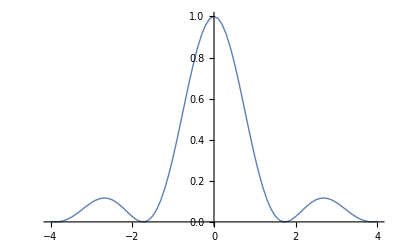

```mathematica
SinglePlot[]@Table[{δ,DetectionValue@Evolution[Hamiltonian@{{{{1,2},{1,0,δ}},1/2}}]},{δ,-4,4,0.1}]
```

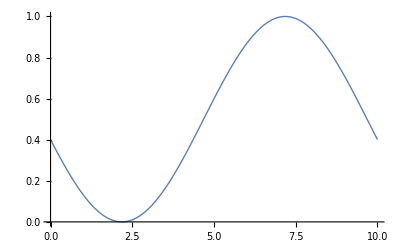

```mathematica
SinglePlot[]@Table[{T,DetectionValue@Evolution[Hamiltonian[{{{{1,2},{1,0,δ}},1/4},{{{1,2},{0,0}},T},{{{1,2},{1,π/2,δ}},1/4}}/.δ->0.1]]},{T,0,10,0.1}]
```

```mathematica
TrappedIon[{1,4},{1,10}];
```

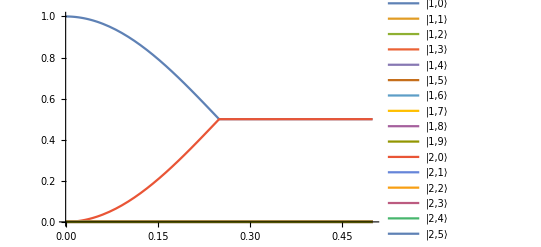

```mathematica
EvolutionPlot[Hamiltonian@{{{{1,2,0},{1,0}},1/4},{{{1,2,0},{1,π/2}},1/4}}]
```

```mathematica
EvolutionPlot[Hamiltonian@{{{1,2,0},{π/2,0}},{{1,2,0},{π/2,π/2}}}]
```

-Graphics-

```mathematica
Frequency[1,3,0]=200;
Frequency[1,3,1]=203;
Frequency[1,3,-1]=197;
Strength[__]=0.8;
```

```mathematica
defs={{{1,3,0},{π,0}},{{{1,3,0},{0.05,0}},{{1,3,1},{0.05,0}},30},{{{1,3,1},{1,0}},1/4}};
ExportWaveString@Wave@defs
```

Frequency (MHz),Duration (us),Amplitude,Phase (Pi),Gap (us),Formula
200.,0.625,1.,0,1.,
200.,0,0.062,0,1.,
203.,0,0.062,0,1.,
0,30.,1.,0,1.,[1 2]
203.,0.25,1.25,0,1.,

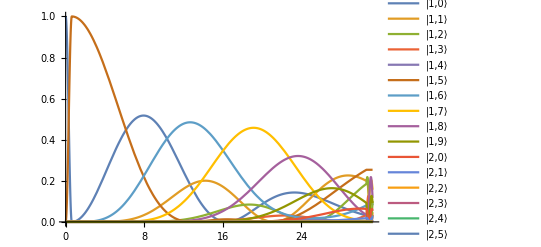

```mathematica
EvolutionPlot[Hamiltonian@defs]
```